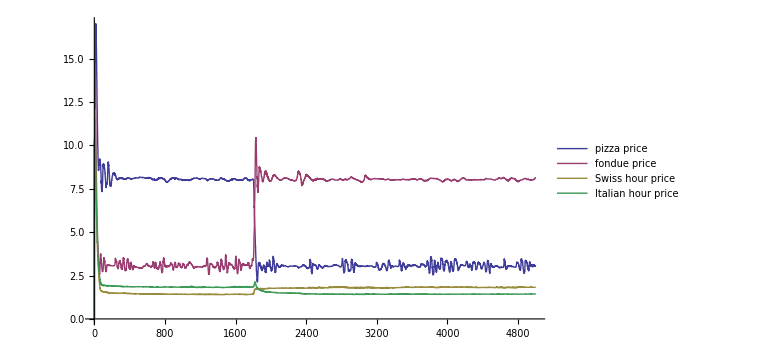

```mathematica
consumerEach = 100;
firmsPerGood = 10;
iterations = 5000;
pizzaPreference = 8;
highProductivity = 6.0;
stockPersistence = 0.98;
smartPriceAdaption = 1; (** 1 or 0 **)

Needs["JLink`"];
ReinstallJava[ClassPath->  NotebookDirectory[] <> "\\..\\bin"];

country = JavaNew["com.abs.World", 24, consumerEach, firmsPerGood, stockPersistence, smartPriceAdaption];
country@updatePreferences[pizzaPreference, pizzaPreference, highProductivity];
country@step[ 1800];
country@updatePreferences[2.0, 2.0, highProductivity];  (**Preference shock **)
country@step[ iterations - 1800];
legend = country@getData[]@getLabels[];
dataT = Transpose[country@getData[]@getAllData[]];

ReleaseJavaObject[country];

selectColumns[data_] := {data[[5]], data[[8]], data[[11]], data[[14]]};
ListLinePlot[selectColumns[dataT], PlotLegends-> selectColumns[legend], PlotRange -> Full, ImageSize->Large]
```